```mathematica
f[x_]:=14 x^3-179 x^2+281x-66
```

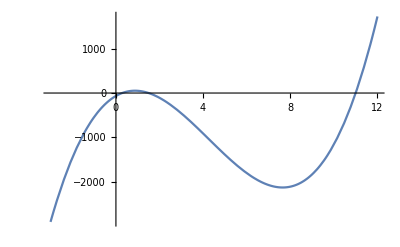

```mathematica
Plot[f[x],{x,-3,12}, AxesOrigin->{0,0}]
```

```mathematica
f[x_]:= 14 x^3-179 x^2+281x-66
prev = 5.01;a=5; b =6; n = 5.99; e = 10^-3; 
hords = {}

Do[n1=n-f[n]/(f[b]-f[n])*(b-n);

If[i≤ 2, AppendTo[hords,n1]];
If[(n1-n)^2/Abs[n1+prev-2*n]<e, Print[n1 , " Шаг:", i]; Break[], prev = n; n=n1 ]
,{i, 1, 100}];

f[n1]
```

{}

1.49917 Шаг:15

0.133941

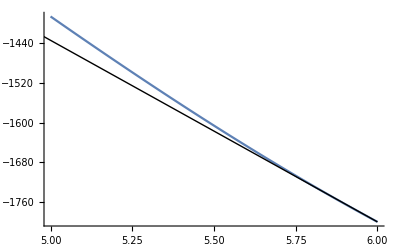

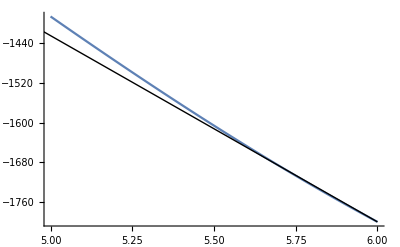

```mathematica
Plot[f[x], {x, 5, 6}, Epilog->Line[{{hords[[1]], f[hords[[1]]]}, {b, f[b]}}]]
Plot[f[x], {x, 5, 6}, Epilog->Line[{{hords[[2]], f[hords[[2]]]}, {b, f[b]}}]]
```

```mathematica
f[x_]:=x^6-x^5-18 x^4+14 x^3+61 x^2-93x+36
```

```mathematica
Solve[f[x]==0]
```

{{x→-3},{x→-3},{x→1},{x→1},{x→1},{x→4}}

```mathematica
NSolve[f[x]==0]
```

{{x→-3.},{x→-3.},{x→1.},{x→1.},{x→1.},{x→4.}}

```mathematica
Roots[f[x]==0,x]
```

x==-3||x==-3||x==1||x==1||x==1||x==4

```mathematica
Factor[f[x]]
```

(-4+x) (-1+x)^3 (3+x)^2

```mathematica
FindRoot[f[x]==0,{x,-2}]
```

{x→-3.}

```mathematica
FindRoot[f[x]==0,{x,0}]
```

{x→0.999996}

```mathematica
FindRoot[f[x]==0,{x,11}]
```

{x→4.}

```mathematica
f[x_]:=5cos(2x+1)=3 x^2+5x-4
```

Set::write: Tag Times in -8.99959\ 5\ cos is Protected.

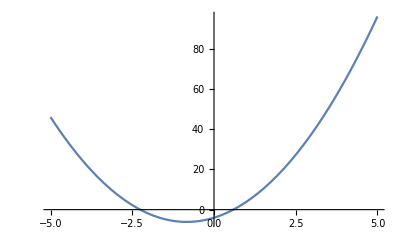

```mathematica
Plot[f[x],{x,-5,5}, AxesOrigin->{0,0}]
```

Set::write: Tag Times in -2.99984\ 5\ cos is Protected.

Set::write: Tag Times in 5\ cos\ (1 + 2\ #1) is Protected.

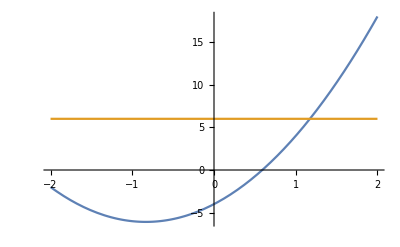

Set::write: Tag Times in 2.6\ 5\ cos is Protected.

Set::write: Tag Times in 5\ cos\ (1 + 2\ #1) is Protected.

Set::write: Tag Times in 2.20816\ 5\ cos is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

0.590667 Шаг:3

```mathematica
f[x_]:=5cos(2x+1)=3 x^2+5x-4
e = 10^-3; n=0.8;
Plot[{f[x], f''[x]}, {x, -2, 2}]
Do[n1=n-f[n]/f'[n];

If[Abs[f[n1]-f[n]]<e, Print[n1 , " Шаг:", i]; Break[], n=n1 ]
,{i, 1, 100}]
```

```mathematica
f[x_]:=5cos(2x+1)=3 x^2+5x-4;
prev = 0.4;e = 10^-3;n=0.5;


Do[n1=n-(n-prev)/(f[n]-f[prev])*f[n];
If[Abs[f[n1]-f[n]]<e, Print[n1 , " Шаг:", i]; Break[],prev=n; n=n1 ]
,{i, 1, 100}]
```

Set::write: Tag Times in 2.\ 5\ cos is Protected.

Set::write: Tag Times in 1.8\ 5\ cos is Protected.

Set::write: Tag Times in 2.\ 5\ cos is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

0.590667 Шаг:4

```mathematica
f[x_]:= 5cos(2x+1)=3 x^2+5x-4;
2/MaxValue[{f'[x],0.5≤x≤1},x]//N
g[x_]:=x-f[x]; n =0.9;
Do[n1=g[n];
If[Abs[f[n1]-f[n]]<e, Print[n1 , " Шаг:", i]; Break[], n=n1 ]
,{i, 1, 100}]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ #1) is Protected.

0.181818

Set::write: Tag Times in 2.8\ 5\ cos is Protected.

Set::write: Tag Times in -3.06\ 5\ cos is Protected.

Set::write: Tag Times in 2.8\ 5\ cos is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

Set::write: Tag Times in 2.18276\ 5\ cos is Protected.

Set::write: Tag Times in 5\ cos\ (1 + 2\ #1) is Protected.

Решение x=0.591378получено на1шаге.

```mathematica
Solve[f[x]==0]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ x) is Protected.

{{x→1/6 (-5-√73)},{x→1/6 (-5+√73)}}

```mathematica
NSolve[f[x]==0]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ x) is Protected.

{{x→-2.25733},{x→0.590667}}

```mathematica
FindRoot[f[x]==0,{x,-2}]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ x) is Protected.

{x→-2.25733}

```mathematica
FindRoot[f[x]==0,{x,0}]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ x) is Protected.

{x→0.590667}

```mathematica
FindRoot[f[x]==0,{x,1}]
```

Set::write: Tag Times in 5\ cos\ (1 + 2\ x) is Protected.

{x→0.590667}

```mathematica
f[x_,y_]=((x+1)^2)^(1/3)+((y-3)^2)^(1/3)-4
```

-4+((1+x)^2)^(1/3)+((-3+y)^2)^(1/3)

```mathematica
g[x_,y_]=3 x^2-5 y^2-15
```

-15+3 x^2-5 y^2

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-3,4},{y,-4,4}, Axes->True,
Frame->False,ImageSize->Small]
gr2=ContourPlot[g[x,y]==0,{x,-3,4},{y,-4,4}, Axes->True,
Frame->False,ImageSize->Small]
```

-Graphics-

-Graphics-

```mathematica
Show[gr1,gr2,ImageSize-> Large]
```

-Graphics-

```mathematica
FindRoot[f[x,y]==0,g[x,y]==0,{x,-1},{y,2}]
```

FindRoot::fdss: Search specification g[x, y] == 0 should be a list with 1 to 5 elements.

FindRoot[f[x,y]==0,g[x,y]==0,{x,-1},{y,2}]